# Traditional EWS on bifurcation plane of Ricker model

## Setup

```mathematica
(* Set Directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fish_project"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};

(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure parameters *)
labelPos={0.06,0.9};
labels=Alphabet[];
padding={{40,90},{40,25}};
```

```mathematica
(* get package for user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl"];
```

## Analysis of Deterministic Ricker

```mathematica
(* N_t+1 = f(N_t) *)
Clear[funDet,r,k,f,h,pop]
funDet[r_,k_,f_,h_,pop_]:=pop*Exp[r(1-pop/k)]-f pop^2 / (pop^2+h^2)
funDet[r,k,f,h,pop]
```

ⅇ^((1-pop/k) r) pop-(f pop^2)/(h^2+pop^2)

```mathematica
k=10; (* carrying capacity *)
p=2;(* exponent for sigmoid functional response *)
h=0.75; (* half-saturation rate *)
```

```mathematica
(* for a particular value of r and h *)
r=1; (* growth rate *)
f=2; (* grazing rate *)
```

```mathematica
(* find equilibria *)
equilibs=NSolve[funDet[r,k,f,h,pop]-pop==0&&(0≤pop≤20),pop]
```

{{pop→0.},{pop→7.71398}}

```mathematica
(* define Jacobian *)
Clear[jac]
jac[pop_,r_,f_]=D[funDet[r,k,f,h,pop],pop]
```

ⅇ^(1-pop/10)-1/10 ⅇ^(1-pop/10) pop+(4 pop^3)/((0.5625+pop^2)^2)-(4 pop)/(0.5625+pop^2)

```mathematica
(* determine stability *)
evals=Table[jac[pop/.equilibs[[i]],r,f],{i,1,Length[equilibs]}]
```

{2.71828,0.282506}

```mathematica
(* find index of stable state *)
equiIndex=Position[evals,Max[Select[evals,-1<#<1&]]]//Flatten
```

{2}

```mathematica
(* select stable equilibrium point *)
equiStable=pop/.equilibs[[equiIndex]][[1]]
```

7.71398

### Find bifurcation curves

#### Import data (simulated below)

```mathematica
(* import fold vals data *)
foldVals=Import["data/sim_data/foldVals.csv"];

(* import hopf vals data *)
hopfVals=Import["data/sim_data/hopfVals.csv"];
```

#### Create function to find equilibria and their eigenvalues

```mathematica
(* output has form {equilibria, evals} *)
```

```mathematica
Clear[equiEvals]
equiEvals[r_,f_]:=Module[{k,h,equilibs,equilibList,output,evals},
(* fixed parameter values *)
k=10;
h=0.75;
(* evolution function *)
Clear[funDet,r0,k0,f0,h0,pop0];
funDet[r0_,k0_,f0_,h0_,pop0_]:=pop0*Exp[r0(1-pop0/k0)]-f0 pop0^2 / (pop0^2+h0^2);
(* find equilibria *)
equilibs=NSolve[funDet[r,k,f,h,pop]-pop==0&&(0≤pop≤30),pop];
(* put them into list form *)
equilibList=Table[pop/.equilibs[[i]],{i,1,Length[equilibs]}]//Flatten;
(* define Jacobian *)
Clear[jac];
jac[pop_]=D[funDet[r,k,f,h,pop],pop];
(* determine stability of equilibria *)
evals=jac[equilibList];
(* export equilibria and evals *)
output={equilibList,evals}
]
```

#### Increment r to find Hopf

```mathematica
(*(* create data grid to store hopf bifurcation values.  *)
fVals=Range[0,25,0.5];
hopfVals={fVals,ConstantArray[0,Length[fVals]]};*)
```

```mathematica
(*rVals=Range[1.9,5,0.0001];*)
```

```mathematica
(*(* loop through f values *)
For[j=1,j≤Length[fVals],j++,
f=fVals[[j]];
(* initialise *)
If[j==1,i=1];
eval=0;
While[-0.99<=eval≤0.99,
Clear[equilibList,evals];
{equilibList,evals}=equiEvals[rVals[[i]],f];
(* index for stable equilibrium *)
equiIndex=Position[equilibList,Max[equilibList]][[1,1]];
(* assign eigenvalue *)
eval=evals[[equiIndex]];
(* increment i *)
i=i+1
];

(* assign r value to hopf vals grid *)
hopfVals[[2,j]]=rVals[[i]];
(* print complete *)
Print["f = "<>ToString[fVals[[j]]]<>" complete"];
]*)
```

```mathematica
(*evals*)
```

```mathematica
(*equiEvals[2.5,9]*)
```

```mathematica
(*hopfVals//MatrixForm*)
```

```mathematica
(*(* export hopf bifurcation vals *)
Export["data/sim_data/hopfVals.csv",hopfVals];
*)
```

#### Increment r to find point of stable node to stable spiral

```mathematica
(* create data grid  *)
fVals=Range[0,25,0.5];
boundaryVals={fVals,ConstantArray[0,Length[fVals]]};
```

```mathematica
rVals=Range[0.5,3,0.01];
```

```mathematica
(* loop through f values *)
For[j=1,j≤Length[fVals],j++,
f=fVals[[j]];
(* initialise *)
If[j==1,i=1];
eval=0;
While[eval≥0,
Clear[equilibList,evals];
{equilibList,evals}=equiEvals[rVals[[i]],f];
(* index for stable equilibrium *)
equiIndex=Position[equilibList,Max[equilibList]][[1,1]];
(* assign eigenvalue *)
eval=evals[[equiIndex]];
(* increment i *)
i=i+1
];

(* assign r value to hopf vals grid *)
boundaryVals[[2,j]]=rVals[[i]];
]
```

Part::partw: Part 252 of {0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,«5»,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,«201»} does not exist.

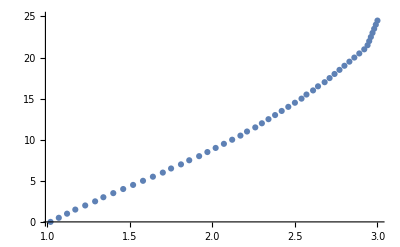

```mathematica
ListPlot[Transpose[Reverse[boundaryVals]],PlotRange->{0,25}]
```

```mathematica
(* export hopf bifurcation vals *)
Export["data/sim_data/boundaryVals.csv",boundaryVals];
```

#### Increment F to find Fold (long sim)

```mathematica
(*(* create data grid to store hopf bifurcation values.  *)
rVals=Range[0.1,3,0.1];
foldVals={rVals,ConstantArray[0,Length[rVals]]};*)
```

```mathematica
(*fVals=Range[0.1,25,0.0001];*)
```

```mathematica
(*(* loop through r values *)
For[j=1,j≤Length[rVals],j++,
r=rVals[[j]];
(* initialise - note that as we go up in r values, the fold bif will increase in value, so no need to reset i to zero each time - keep incrementing *)
If[j==1,i=1];
eval=0;
While[-0.99<=eval≤0.99,
Clear[equilibList,evals];
{equilibList,evals}=equiEvals[r,fVals[[i]]];
(* index for stable equilibrium *)
equiIndex=Position[equilibList,Max[equilibList]][[1,1]];
(* assign eigenvalue *)
eval=evals[[equiIndex]];
(* increment i *)
i=i+1
];

(* assign f value to fold vals grid *)
foldVals[[2,j]]=fVals[[i]];
(* print complete *)
Print["r = "<>ToString[rVals[[j]]]<>" complete"];
]*)
```

```mathematica
(*(* export fold bifurcation vals *)
Export["data/sim_data/foldVals.csv",foldVals];*)
```

#### Plot Region

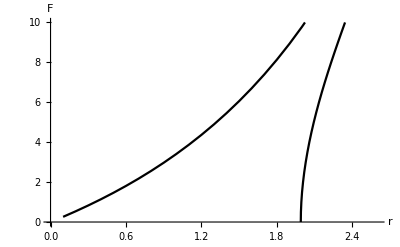

```mathematica
plotRegionStable=ListLinePlot[{Transpose[Reverse[hopfVals]],Transpose[foldVals]},
PlotRange->{{0,2.6},{0,10}},
PlotStyle->{Black,Black,{Black,Dashed}},
LabelStyle->14,
AxesLabel->{"r","F"}]
```

```mathematica
plotRegionStableAnnote=ListLinePlot[{Transpose[Reverse[hopfVals]],Transpose[foldVals],Transpose[Reverse[boundaryVals]]},
PlotStyle->{Black,Black,{Black,Dashed}},
Frame->True,
PlotRange->{{0.1,2.4},{0,10}},
LabelStyle->14,
AspectRatio->0.7,
FrameLabel->{"r","F"},
ImageSize->400,
ImagePadding->padding,
Epilog->{Text[Style["Flip",12],Scaled[{0.92,0.18}]],
Text[Style["Fold",12],Scaled[{0.35,0.52}]],
Text[Style["Stable\nNode",12],Scaled[{0.34,0.12}]],
Text[Style["Stable\nSpiral",12],Scaled[{0.65,0.12}]],
Arrowheads[{0,0.04}],
Arrow[{Scaled[{0.47,0.33}],Scaled[{0.38,0.47}]}],
Arrow[{Scaled[{0.77,0.1}],Scaled[{0.9,0.1}]}],
Text[Style[labels[[1]],14,Bold],Scaled[labelPos]]}
]
```

-Graphics-

## Simulate Ricker Model

### Parameters for simulation

```mathematica
{r,f}={2,0}; (* temporary growth rate, grazing rate *)
k=10; (* carrying capacity *)
p=2;(* exponent for sigmoid functional response *)
h=0.75; (* half-saturation rate *)

sr=0; (* process error on r - demeographic noise *)
se=0.01;(* environmental noise *)
su=0; (* measurement error - observational noise *)

tmax=400; (* number of time steps for each realisation *)
```

### Single Simulation

#### Simulation

```mathematica
(* create data array for simulation *)
x=ConstantArray[0,tmax+1];
```

```mathematica
(* set initial condition to stable equilibrium *)
x[[1]]=Max[equiEvals[r,f][[1]]]
```

10.

```mathematica
(* N_t+1 = f(N_t) *)
Clear[fun]
fun[r_,k_,f_,h_,noise_,pop_]:=pop*Exp[r(1-pop/k)+se noise]-f pop^2 / (pop^2+h^2)
```

```mathematica
(* normal random variables mean zero variance 1 for noise *)
noise=RandomVariate[NormalDistribution[0,1],tmax];
```

```mathematica
noise[[1;;10]]
```

{0.0322245,0.703778,-0.34407,1.05512,-0.543082,1.04943,0.963635,-0.489841,-0.371079,-1.46596}

```mathematica
(* begin iterations *)
For[i=1,i≤tmax,i++,
x[[i+1]]=fun[r,k,f,h,noise[[i]],x[[i]]];
(* make sure noise does not make x negative *)
If[x[[i+1]]<0,x[[i+1]]=0];
]
```

#### Analysis of simulation

```mathematica
(* check out power spectrum of simulations *)
```

```mathematica
pSpec=TBPowerSpecWelch[{x-Mean[x],1,hamLength,hamOffset}];
```

```mathematica
fitUnimodal=NonlinearModelFit[Transpose[pSpec],c*(1/(ω^2+λ^2)),{c,λ},ω,MaxIterations->10000];
fitBimodal=NonlinearModelFit[Transpose[pSpec],c*(1/((ω-ω0)^2+λ^2)+1/((ω+ω0)^2+λ^2)),{c,λ,ω0},ω,MaxIterations->10000];
(* parameter value estimates for each fit *)
{cUni,λUni}=fitUnimodal["ParameterTableEntries"][[;;,1]];
{cBi,λBi,ω0Bi}=fitBimodal["ParameterTableEntries"][[;;,1]];
(* R^2 error from fitting *)
rSquareUnimodal=fitUnimodal["RSquared"];
rSquareBimodal=fitBimodal["RSquared"];
rSquareRatio=rSquareUnimodal/rSquareBimodal;
(* AIC scores from fitting *)
aicUnimodal=fitUnimodal["AIC"];
aicBimodal=fitBimodal["AIC"];
(* AIC weights *)
aicDiff1=aicUnimodal-Min[aicUnimodal,aicBimodal];
aicDiff2=aicBimodal-Min[aicUnimodal,aicBimodal];
likelihood1=Exp[-(1/2)*aicDiff1];
likelihood2=Exp[-(1/2)*aicDiff2];
foldAICweight=likelihood1/(likelihood1+likelihood2);
hopfAICweight=likelihood2/(likelihood1+likelihood2);
```

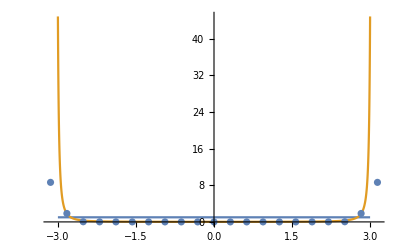

```mathematica
Show[Plot[{fitUnimodal[x],fitBimodal[x]},{x,-3,3},PlotRange->All],ListPlot[Transpose[pSpec],PlotRange->{0,0.012}]]
```

```mathematica
rSquareBimodal
```

0.998833

```mathematica
rSquareUnimodal
```

0.135995

```mathematica
rSquareRatio
```

0.136154

```mathematica
?TBFitSpec
```

TBFitSpec[pSpec] fits three power spectrum models to the input: unimodal, bimodal and flat (null).
pSpec = {freqVals,powerVals}
Outputs {foldWeight, hopfWeight, nullWeight}
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense);

```mathematica
TBFitSpec[pSpec]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{2.16081×10^-30,1.,6.10481×10^-30}

```mathematica
TBCoherFactor[pSpec]
```

8.62921

### Multiple simulations with different parameter values (r and F)

#### Construct parameter combinations

```mathematica
(* interpolate bifurcation curves - functions take r and give F *)
foldInterpol=Interpolation[Transpose[foldVals]]
```

InterpolatingFunction[{{0.1, 3.}}, <>]

```mathematica
hopfInterpol=Interpolation[Transpose[Reverse[hopfVals]]]
```

InterpolatingFunction[{{1.9902, 3.1404}}, <>]

```mathematica
hopfInterpol
```

InterpolatingFunction[{{1.9902, 3.1404}}, <>]

```mathematica
(* make array of parameter combinations in stable regime *)
rVals=Range[0.1,2.3,0.025];
Clear[fVals]
(* function to select subset of fVals in stable regime given a value of r *)
fVals[r_]:=If[r<2,Range[0,foldInterpol[r]-0.5,0.1],
Range[hopfInterpol[r]+1,foldInterpol[r]-0.5,0.1]];
```

```mathematica
parCombos=Flatten[
Table[{rVals[[i]],fVals[rVals⟦i⟧]⟦j⟧},{i,1,Length[rVals]},{j,1,Length[fVals[rVals⟦i⟧]]}],1];
```

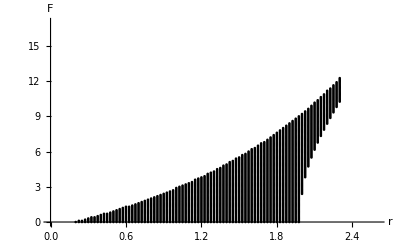

```mathematica
parCombosPlot=ListPlot[parCombos,PlotRange->{{0,2.6},{0,17}},
PlotStyle->Black,
LabelStyle->14,
AxesLabel->{"r","F"}]
```

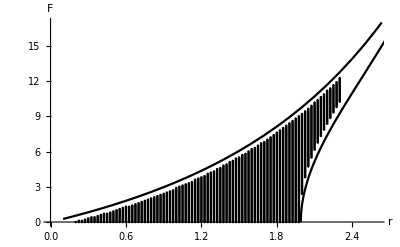

```mathematica
Show[plotRegionStable,parCombosPlot]
```

```mathematica
parCombos//Dimensions
```

{3206,2}

#### Simulate system for each parameter combination

```mathematica
(* create array for simulations *)
seriesArray=ConstantArray[0,{Length[parCombos],tmax+1}];
(* transient time to discard *)
transTime=100;
```

```mathematica
seriesArray//Dimensions
```

{3206,401}

```mathematica
For[i=1,i≤Length[parCombos],i++,
{r,f}=parCombos[[i]];
(* array for trajectory *)
x=ConstantArray[0,tmax+1];
(* set initial condition to stable equilibrium *)
x[[1]]=Max[equiEvals[r,f][[1]]];
(* normal random variables mean zero variance 1 for noise *)
noiseTrans=RandomVariate[NormalDistribution[0,1],transTime];
noise=RandomVariate[NormalDistribution[0,1],tmax];
(* begin simulation *)
(* run transient *)
j=1;
While[j≤transTime,
x[[1]]=fun[r,k,f,h,noiseTrans[[j]],x[[1]]];
(* if x goes negative, terminate *)
If[x[[1]]≤0,x[[1]]=0];
j=j+1;
];
(* record future trajectory *)
For[q=1,q≤tmax,q++,
x[[q+1]]=fun[r,k,f,h,noise[[q]],x[[q]]];
(* make sure noise does not make x negative *)
If[x[[q+1]]<=0,
Print["Parameter combination "<>ToString[parCombos[[i]]]<>" collapsed"];
q=tmax;];];
(* add trajectory to series array *)
seriesArray[[i,;;]]=x;
]
```

```mathematica
(*Export["data/sim_data/stationarySims.csv",seriesArray];*)
```

```mathematica
seriesArray//Dimensions
```

{3206,401}

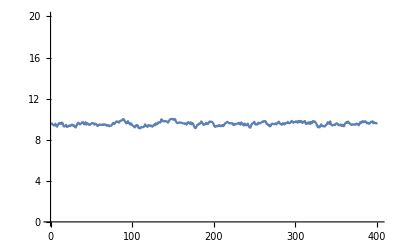

```mathematica
ListLinePlot[seriesArray[[3,;;]],PlotRange->{0,20}]
```

```mathematica
|
```

## Compute EWS

### Parameters for EWS and figures

Note: time-series are stationary so no need for detrending or rolling window - just compute indicator over entire time-series

```mathematica
(* hamming window properties *)
hamLength=20;
hamOffset=5;
```

```mathematica
(* figure parameters *)
colFunction="Automatic";
```

```mathematica
(* define colour function to map normalised metric onto color spectrum *)
Clear[colorfun]
colorfun[metric_]:=ColorData["DarkRainbow"][metric]
```

```mathematica
(* define function to scale list of outputs onto the unit interval such that min value obtains zero and max value obtains 1 - this is for color function *)
Clear[scaleUnitInterval]
scaleUnitInterval[list_]:=Module[{max,min,output},
max=Max[list];
min=Min[list];
output=(list-min)/(max-min)
]
```

```mathematica
seriesArray//Dimensions
```

{3206,401}

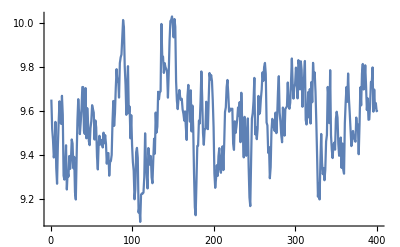

```mathematica
ListLinePlot[seriesArray[[3,;;]]]
```

### Compute traditional EWS

```mathematica
(* standard indicators *)
varVals=Table[Variance[seriesArray[[i,;;]]],{i,1,Length[parCombos]}];
meanVals=Table[Mean[seriesArray[[i,;;]]],{i,1,Length[parCombos]}];
cvVals=varVals/meanVals;
ac1Vals=Table[CorrelationFunction[seriesArray[[i,;;]],1],{i,1,Length[parCombos]}];
ac2Vals=Table[CorrelationFunction[seriesArray[[i,;;]],2],{i,1,Length[parCombos]}];
```

### Variance plots

```mathematica
(*varDensityPlot=ListPlot[Table[Style[parCombos[[i]],colorfun[scaleUnitInterval[varVals]⟦i⟧]],{i,1,Length[parCombos]}],
PlotStyle->PointSize[0.01],
PlotRange->{{0.5,2.6},{0,17}},
LabelStyle->14,
AxesLabel->{"r","F"},
ImageSize->400
];*)
```

```mathematica
(*(* cap the variance values at some max value to see lower trends - make sure to add to legend the max value and up *)
varMax=0.015;
varValsCap=varVals;
For[i=1,i≤Length[varVals],i++,
If[varVals[[i]]≥varMax,varValsCap[[i]]=varMax]]*)
```

```mathematica
(*contourPlotVarTemp=ListContourPlot[Table[Append[parCombos[[i]],varVals[[i]]],{i,1,Length[parCombos]}],
InterpolationOrder->0,
PlotRange->{{0.5,2.6},{0,17}},
LabelStyle->14,
AspectRatio->0.75,
FrameLabel->{"r","F"},
RegionFunction->Function[{x,y,z},(x>2&&hopfInterpol[x]<y<foldInterpol[x]-0.5)||(x≤2&&y<foldInterpol[x]-0.5)]
];*)
```

```mathematica
(*spotPlotVar=Show[varDensityPlot,plotRegionStable];*)
```

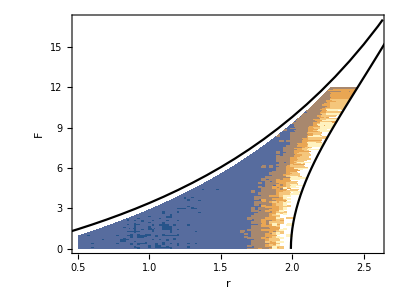

```mathematica
(*contourPlotVar=Show[contourPlotVarTemp,plotRegionStable]*)
```

### CoV plots

```mathematica
(* cap the cov values at some max value to see lower trends - make sure to add to legend the max value and up *)
cvMax=0.004;
cvValsCap=cvVals;
For[i=1,i≤Length[cvVals],i++,
If[cvVals[[i]]≥cvMax,cvValsCap[[i]]=cvMax]]
```

```mathematica
contourPlotCvTemp=ListContourPlot[Table[Append[parCombos[[i]],cvValsCap[[i]]],{i,1,Length[parCombos]}],
InterpolationOrder->0,
PlotRange->{{0.1,2.4},{0,10}},
LabelStyle->14,
AspectRatio->0.7,
FrameLabel->{"r","F"},
ImageSize->400,
ImagePadding->padding,
PlotRangeClipping->False,
ColorFunction->"LakeColors",
RegionFunction->Function[{x,y,z},(x>2&&hopfInterpol[x]<y<foldInterpol[x]-0.3)||(x≤2&&y<foldInterpol[x]-0.3)],
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->"C.V.",
LabelStyle->14,
Ticks->Append[Table[{i,i},{i,Range[0.001,0.003,0.0005]}],{0.0035,"0.0035+"}],
LegendMarkerSize->220],Scaled[{1.01,0.5}]],
Epilog->Text[Style[labels[[2]],14,Bold],Scaled[labelPos]]
];
```

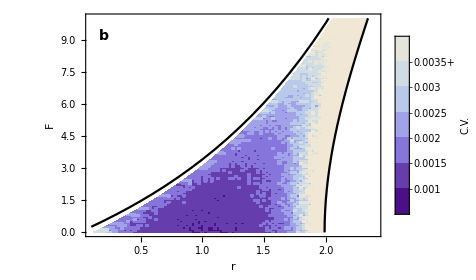

```mathematica
contourPlotCv=Show[contourPlotCvTemp,plotRegionStable]
```

### AC1 plots

```mathematica
(* cap the ac values at some max value to see lower trends - make sure to add to legend the max value and up *)
ac1Max=1;
ac1ValsCap=ac1Vals;
For[i=1,i≤Length[ac1Vals],i++,
If[ac1Vals[[i]]≥ac1Max,ac1ValsCap[[i]]=ac1Max]]
```

```mathematica
contourPlotAc1Temp=ListContourPlot[Table[Append[parCombos[[i]],ac1Vals[[i]]],{i,1,Length[parCombos]}],
InterpolationOrder->0,
PlotRange->{{0.1,2.4},{0,10}},
PlotRangeClipping->False,
LabelStyle->14,
AspectRatio->0.7,
FrameLabel->{"r","F"},
ImageSize->400,
ImagePadding->padding,
ColorFunction->"LakeColors",
RegionFunction->Function[{x,y,z},(x>2&&hopfInterpol[x]<y<foldInterpol[x]-0.3)||(x≤2&&y<foldInterpol[x]-0.3)],
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->"AC(1)",
LabelStyle->14,
(*Ticks->Append[Table[{i,i},{i,Range[0.01,0.06,0.01]}],{0.07,"0.07 +"}],*)
LegendMarkerSize->220],Scaled[{1.01,0.5}]],
Epilog->Text[Style[labels[[3]],14,Bold],Scaled[labelPos]]
];
```

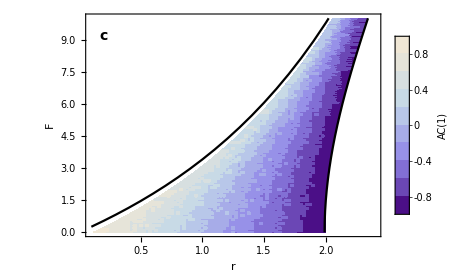

```mathematica
contourPlotAc1=Show[contourPlotAc1Temp,plotRegionStable]
```

### AC2 plots

```mathematica
(* cap the ac values at some max value to see lower trends - make sure to add to legend the max value and up *)
ac2Max=0.6;
ac2ValsCap=ac2Vals;
For[i=1,i≤Length[ac2Vals],i++,
If[ac2Vals[[i]]≥ac2Max,ac2ValsCap[[i]]=ac2Max]]
```

```mathematica
contourPlotAc2Temp=ListContourPlot[Table[Append[parCombos[[i]],ac2ValsCap[[i]]],{i,1,Length[parCombos]}],
InterpolationOrder->0,
PlotRange->{{0.1,2.4},{0,10}},
LabelStyle->14,
AspectRatio->0.7,
FrameLabel->{"r","F"},
ImageSize->400,
PlotRangeClipping->False,
ImagePadding->padding,
ColorFunction->"LakeColors",
RegionFunction->Function[{x,y,z},(x>2&&hopfInterpol[x]<y<foldInterpol[x]-0.3)||(x≤2&&y<foldInterpol[x]-0.3)],
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->"AC(2)",
LabelStyle->14,
(*Ticks->Append[Table[{Round[i,0.1],ToString[i]},{i,Range[-0.1,0.4,0.1]}],{0.5,"0.5 +"}],*)
LegendMarkerSize->220],Scaled[{1.01,0.5}]],
Epilog->{Text[Style[labels[[4]],14,Bold],Scaled[labelPos]],
Text[Style["+",14],Scaled[{1.21,0.88}]]}
];
```

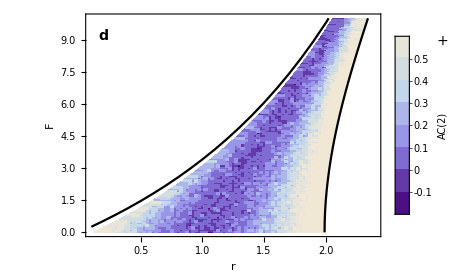

```mathematica
contourPlotAc2=Show[contourPlotAc2Temp,plotRegionStable,PlotRange->{{0.1,2.4},{0,10}}]
```

### Plot Grid

```mathematica
plotGridBifPlane=Grid[{{plotRegionStableAnnote,contourPlotCv},{contourPlotAc1,contourPlotAc2}},Spacings->{-0.2,-0.2}]
```

-Graphics-

```mathematica
Export["figures/ews_trad_planes.png",plotGridBifPlane,ImageResolution->200];
```

## Check points that disagree

```mathematica
(*psdMetData=Table[Append[parCombos[[i]],psdMetric[[i]]],{i,1,Length[parCombos]}];*)
```

```mathematica
(*psdMetData[[1;;10]]*)
```

```mathematica
(*Position[{2,4,6,8,10},_?(#>7&)]*)
```

```mathematica
(*psdMetData[[3]]*)
```

```mathematica
(*psdMetData[[1;;10]]*)
```

```mathematica
(*failPos=Position[psdMetData,_?(#[[1]]<1&&#[[2]]≤2&&#[[3]]≥0.8&)]//Quiet//Flatten*)
```

```mathematica
(*parCombos[[failPos]]//TableForm*)
```